```mathematica
Clear[minx,miny,maxx,maxy]
minx = -2;
miny = -2;
maxx = 2;
maxy = 2;
```

```mathematica
Clear[sol,x,y,t,σ]
σ = -1;
sol[x0_,y0_] := NDSolve[
{x'[t] == (σ+3)*x[t] + 4*y[t],
y'[t]==-9/4*x[t] -(σ-3)*y[t],
x[0]==x0,y[0]==y0},
{x,y},{t,0,10}]
```

```mathematica
initialCond = Join[
Table[{minx , y } , {y,miny , maxy,0.1}],
Table[{x , miny},{x , minx , maxx,0.1}],
Table[{x,maxy},{x,minx , maxx,0.1}],
Table[{maxx, y} , {y, miny , maxy,0.1}]
];
```

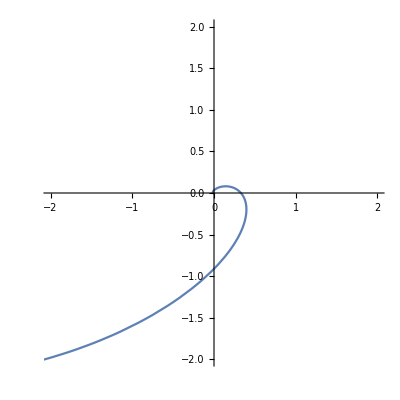

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/. sol[initialCond[[50,1]],initialCond[[50,2]]]],
{t,0,5}, PlotRange->{{minx,maxx},{miny,maxy}}]
```

```mathematica
p2 = Show[
Table[
ParametricPlot[
Evaluate[{x[t], y[t]}/.sol[initialCond[[i,1]], initialCond[[i,2
]]]],{t,0,5},PlotRange->{{minx,maxx},{miny,maxy}}],{i,1,Length[initialCond]}]
]
```

-Graphics-

```mathematica
Show[p2,StreamPlot[{(σ+3)*x + 4*y,-9/4*x -(σ-3)*y},{x,-2,2},{y,-2,2}],PlotRange->{{minx,maxx},{miny,maxy}}]
```

-Graphics-